# Happy Numbers

```mathematica
Get["/home/blmayer/doctorate/thesis/visibility.mx"]
```

```mathematica
numbers=happies[[;;20000]];
```

```mathematica
series=Table[{x,Length@Divisors[x]},{x,numbers}]
```

{{1,1},{7,2},{10,4},{13,2},{19,2},{23,2},{28,6},{31,2},{32,6},{44,6},{49,3},{68,6},{70,8},{79,2},{82,4},{86,4},{91,4},{94,4},19964,{135372,24},{135374,8},{135376,10},{135381,4},{135385,4},{135392,12},{135407,8},{135414,12},{135419,4},{135426,8},{135437,4},{135441,12},{135446,4},{135462,16},{135464,32},{135470,32},{135473,8},{135491,4}}
 |  |  |  |

```mathematica
orbit[x_]:=Block[{d=0,n=x},
While[n>2,n=Length@Divisors[n];d+=1;];
Return[d]
]
```

## Divisors

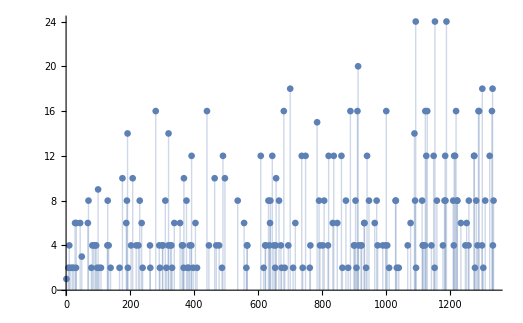

```mathematica
ListPlot[series[[;;200]],Filling->Axis]
```

### Convergence of mean degree and mean distance

```mathematica
sdl[vals_List]:=Block[{diffs,counts,Hmax,H,delta},
diffs=Differences[vals];
counts=Counts[#]/Length@diffs&@diffs;
Hmax=Log[Length@counts];
H=-Total[# Log[#]&/@counts]//N;
delta=H/Hmax;
{4 delta(1-delta),delta}//N
]
```

```mathematica
sdl[series]
```

{0.549343,0.835655}

## Visibility graphs

## Natural Visibility

```mathematica
happyNVLinks=naturalVisibility[series];
```

```mathematica
happyNVGraph=Graph[happyNVLinks,DirectedEdges->False,VertexLabels->"Name",GraphLayout->"CircularEmbedding"];
```

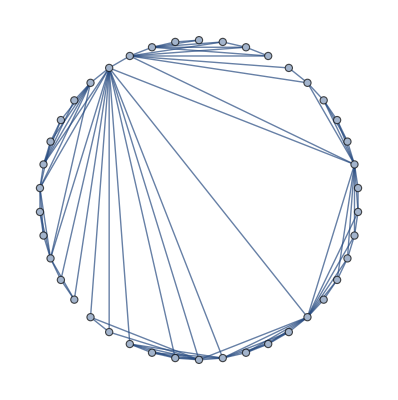

```mathematica
Graph[happyNVLinks[[;;100]],DirectedEdges->False,GraphLayout->"CircularEmbedding"]
```

```mathematica
happyNVDegrees=Counts[VertexDegree[happyNVGraph]]/Length@VertexDegree[happyNVGraph]
```

<|2→303/2500,6→387/4000,3→3197/20000,4→27/160,8→253/5000,12→169/10000,15→89/10000,9→339/10000,5→86/625,7→1359/20000,19→53/10000,16→157/20000,11→107/5000,24→29/10000,23→29/10000,46→9/20000,10→69/2500,13→8/625,14→233/20000,17→137/20000,18→4/625,30→33/20000,35→1/1000,28→37/20000,29→19/20000,63→3/20000,26→27/20000,27→37/20000,33→7/10000,22→2/625,20→41/10000,25→7/4000,21→7/2000,39→13/20000,31→3/2500,32→1/1250,41→7/20000,57→1/5000,77→1/20000,42→9/20000,43→9/20000,54→1/5000,56→1/10000,37→13/20000,36→3/5000,76→1/10000,112→1/20000,34→21/20000,40→1/2500,38→1/2500,51→1/4000,44→1/5000,59→1/10000,60→1/10000,52→1/20000,45→1/10000,65→3/20000,80→1/20000,58→1/20000,72→1/10000,101→1/20000,53→3/20000,48→1/10000,49→1/10000,50→1/10000,55→1/20000,47→1/20000|>

```mathematica
happyNVDegrees[1]=.
```

```mathematica
data=Table[{x,happyNVDegrees[x]},{x,Keys[happyNVDegrees]}];
happyNVNlm=NonlinearModelFit[data,c k^-γ E^(-d k),{{γ,2},{c,3},{d,0}},k]
```

FittedModel[0.0973184 ⅇ^(-0.675061 k) k^2.30214]

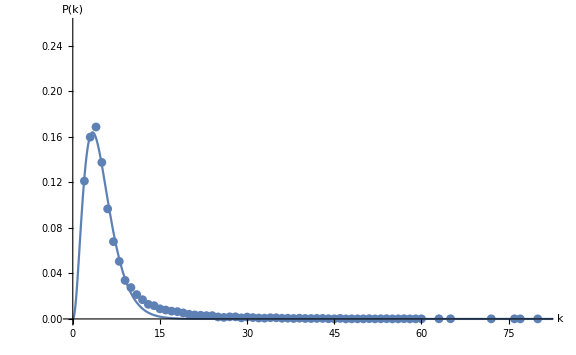

```mathematica
happyNVPlot=Show[
ListPlot[happyNVDegrees,PlotRange->{{0,81},{0,0.259}},AxesOrigin->{0,0}],
Plot[happyNVNlm[x],{x,0,Max[Keys[happyNVDegrees]]},PlotRange->{{0,81},{0,0.26}},AxesOrigin->{0,0}],
AxesLabel-> {Style["k",36, Italic],Style["P(k)", 36,Italic]},LabelStyle->20,ImageSize->Large
]
```

```mathematica
happyNVNlm["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
γ | -2.30214 | 0.109714 | {-2.52132,-2.08296}
c | 0.0973184 | 0.00511548 | {0.087099,0.107538}
d | 0.675061 | 0.0256677 | {0.623783,0.726338}

```mathematica
TableForm[Flatten[{"natural visibility",Mean@ VertexDegree[happyNVGraph]//N,MeanGraphDistance[happyNVGraph]//N,
GlobalClusteringCoefficient[happyNVGraph]//N,Mean[happyNVNlm["FitResiduals"]^2],ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@happyNVNlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}],TableHeadings->{{"algo","⟨k⟩","⟨l_min⟩","C_c","⟨e^2⟩","γ","C","δ"}, None},TableDirections->Row]
```

algo | ⟨k⟩ | ⟨l_min⟩ | C_c | ⟨e^2⟩ | γ | C | δ
natural visibility | 6.5896 | 6.84412 | 0.354645 | 0.0000115452 | -2.30214 ± 0.219179 | 0.0973184 ± 0.0102194 | 0.675061 ± 0.0512771

## Horizontal Visibility

```mathematica
happyHVLinks=horizontalVisibility[series];
```

```mathematica
happyHVGraph=Graph[happyHVLinks,DirectedEdges->False,VertexLabels->"Name",GraphLayout->"CircularEmbedding"];
```

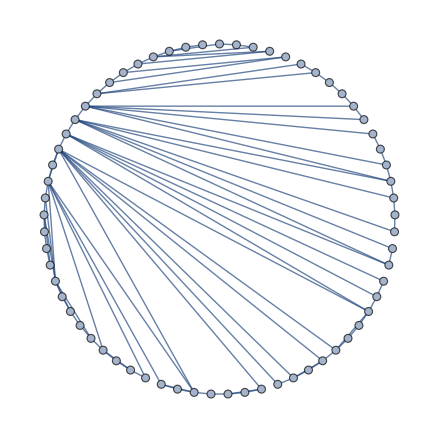

```mathematica
Graph[happyHVLinks[[;;100]],DirectedEdges->False,GraphLayout->"CircularEmbedding"]
```

```mathematica
happyHVDegrees=Counts[VertexDegree[happyHVGraph]]/Length@VertexDegree[happyHVGraph]
```

<|1→1/10000,2→263/625,3→137/625,4→177/1250,7→639/20000,6→39/800,5→421/5000,10→149/20000,8→403/20000,9→53/4000,12→53/20000,11→27/5000,13→19/10000,14→19/20000,15→1/1250,16→9/20000,17→3/10000,18→1/20000,20→1/20000|>

```mathematica
happyHVDegrees[1]=.
```

```mathematica
data=Table[{x,happyHVDegrees[x]},{x,Keys[happyHVDegrees]}];
happyHVNlm=NonlinearModelFit[data,c k^-γ E^(-d k),{{γ,2},{c,3},{d,0}},k]
```

FittedModel[(1.32232 ⅇ^(-«19» k))/k^0.67699]

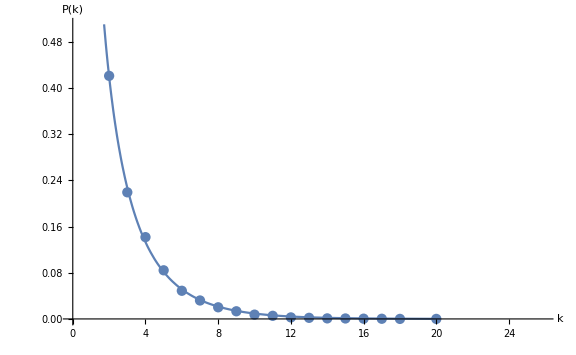

```mathematica
happyHVPlot=Show[
ListPlot[happyHVDegrees,PlotRange->{{0,25.9},{0,.51}},AxesOrigin->{0,0}],Plot[happyHVNlm[x],{x,0,Max[Keys[happyHVDegrees]]},PlotRange->{{0,25},{0,0.51}},AxesOrigin->{0,0}],
AxesLabel-> {Style["k",36, Italic],Style["P(k)", 36,Italic]},LabelStyle->20,ImageSize->Large
]
```

```mathematica
happyHVNlm["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
γ | 0.67699 | 0.105101 | {0.452973,0.901008}
c | 1.32232 | 0.0292029 | {1.26008,1.38457}
d | 0.339599 | 0.0323713 | {0.270601,0.408597}

```mathematica
TableForm[
Flatten[{"horizontal visibility",Mean@ VertexDegree[happyHVGraph]//N,MeanGraphDistance[happyHVGraph]//N,
GlobalClusteringCoefficient[happyHVGraph]//N,Mean[happyHVNlm["FitResiduals"]^2],ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@happyHVNlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}],TableHeadings->{{"algo","⟨k⟩","⟨l_min⟩","C_c","⟨e^2⟩","γ","C","δ"},None},TableDirections->Row]
```

algo | ⟨k⟩ | ⟨l_min⟩ | C_c | ⟨e^2⟩ | γ | C | δ
horizontal visibility | 3.5132 | 15.2123 | 0.271626 | 8.99209×10^-6 | 0.67699 ± 0.224018 | 1.32232 ± 0.0622446 | 0.339599 ± 0.0689978

## Orbits

```mathematica
orbits=Table[{x,orbit[x]},{x,numbers}];
```

```mathematica
sdl[orbits]
```

{0.621853,0.807468}

## Visibility graphs

## Natural Visibility

```mathematica
happyOrbitsNVLinks=naturalVisibility[orbits];
```

```mathematica
happyOrbitsNVGraph=Graph[happyOrbitsNVLinks,DirectedEdges->False,GraphLayout->"CircularEmbedding"];
```

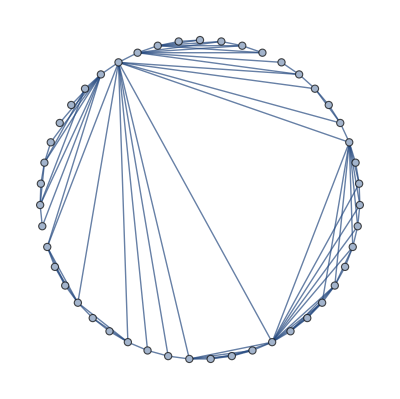

```mathematica
Graph[happyOrbitsNVLinks[[;;100]],DirectedEdges->False,GraphLayout->"CircularEmbedding"]
```

```mathematica
happyOrbitsNVDegrees=Counts[VertexDegree[happyOrbitsNVGraph]]/Length@VertexDegree[happyOrbitsNVGraph]//KeySort
```

<|2→1797/10000,3→4317/20000,4→921/5000,5→159/1250,6→413/5000,7→283/5000,8→439/10000,9→319/10000,10→459/20000,11→31/2000,12→117/10000,13→133/20000,14→101/20000,15→2/625,16→39/20000,17→31/20000,18→3/4000,19→11/20000,20→1/5000,21→1/4000,22→1/5000,23→3/20000,24→1/5000,25→3/20000,26→1/5000,27→1/4000,28→1/10000,29→1/10000,30→3/20000,31→1/10000,32→7/20000,33→1/5000,34→1/10000,35→1/10000,36→1/5000,37→1/10000,38→1/20000,39→1/20000,40→3/20000,41→1/10000,42→1/10000,43→1/20000,47→1/10000,49→1/10000,50→1/20000,51→1/10000,52→1/20000,53→1/20000,55→1/10000,56→1/10000,57→1/20000,58→1/10000,59→1/4000,60→1/20000,61→1/10000,62→1/20000,63→1/20000,64→1/20000,65→1/20000,68→3/20000,69→1/10000,71→1/20000,72→1/20000,73→1/20000,74→1/20000,75→1/10000,76→1/20000,77→1/10000,78→1/20000,79→1/10000,80→1/20000,81→3/20000,82→1/20000,85→1/10000,89→3/20000,90→3/20000,91→1/10000,94→1/20000,95→1/20000,96→1/20000,102→1/20000,103→3/20000,104→1/10000,105→1/20000,106→1/20000,109→1/20000,110→1/20000,111→1/20000,112→1/20000,120→1/10000,123→1/20000,131→1/20000,134→1/20000,135→1/20000,136→1/20000,140→1/20000,161→1/20000,164→1/10000,183→1/20000,192→1/20000,235→1/20000,246→1/20000,517→1/20000,785→1/20000|>

```mathematica
happyOrbitsNVDegrees[1]=.
```

```mathematica
data=Table[{x,happyOrbitsNVDegrees[x]},{x,Keys[happyOrbitsNVDegrees]}];
happyOrbitsNVNlm=NonlinearModelFit[data,c k^-γ E^(-d k),{{γ,2},{c,3},{d,0}},k]
```

FittedModel[0.193115 ⅇ^(-0.754397 k) k^2.12168]

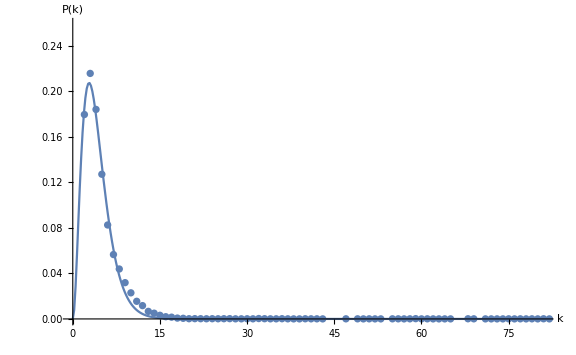

```mathematica
happyOrbitsNVPlot=Show[
ListPlot[happyOrbitsNVDegrees,PlotRange->{{0,81},{0,0.259}},AxesOrigin->{0,0}],
Plot[happyOrbitsNVNlm[x],{x,0,Max[Keys[happyOrbitsNVDegrees]]},PlotRange->{{0,81},{0,0.26}},AxesOrigin->{0,0}],
AxesLabel-> {Style["k",36, Italic],Style["P(k)", 36,Italic]},LabelStyle->20,ImageSize->Large
]
```

```mathematica
happyOrbitsNVNlm["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
γ | -2.12168 | 0.0820926 | {-2.28453,-1.95883}
c | 0.193115 | 0.00576069 | {0.181687,0.204542}
d | 0.754397 | 0.0217104 | {0.71133,0.797465}

```mathematica
TableForm[Flatten[{"natural visibility",Mean@ VertexDegree[happyOrbitsNVGraph]//N,MeanGraphDistance[happyOrbitsNVGraph]//N,
GlobalClusteringCoefficient[happyOrbitsNVGraph]//N,Mean[happyOrbitsNVNlm["FitResiduals"]^2],ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@happyOrbitsNVNlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}],TableHeadings->{{"algo","⟨k⟩","⟨l_min⟩","C_c","⟨e^2⟩","γ","C","δ"}, None},TableDirections->Row]
```

algo | ⟨k⟩ | ⟨l_min⟩ | C_c | ⟨e^2⟩ | γ | C | δ
natural visibility | 5.3117 | 54.5357 | 0.124025 | 6.82896×10^-6 | -2.12168 ± 0.16285 | 0.193115 ± 0.0114277 | 0.754397 ± 0.0430676

## Horizontal Visibility

```mathematica
happyOrbitsHVLinks=horizontalVisibility[series];
```

```mathematica
happyOrbitsHVGraph=Graph[happyOrbitsHVLinks,DirectedEdges->False,GraphLayout->"CircularEmbedding"];
```

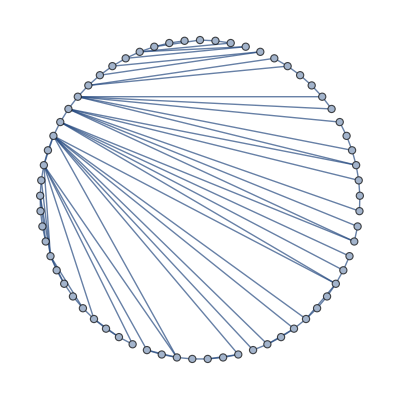

```mathematica
Graph[happyOrbitsHVLinks[[;;100]],DirectedEdges->False,GraphLayout->"CircularEmbedding"]
```

```mathematica
happyOrbitsHVDegrees=Counts[VertexDegree[happyOrbitsHVGraph]]/Length@VertexDegree[happyOrbitsHVGraph]
```

<|1→1/10000,2→263/625,3→137/625,4→177/1250,7→639/20000,6→39/800,5→421/5000,10→149/20000,8→403/20000,9→53/4000,12→53/20000,11→27/5000,13→19/10000,14→19/20000,15→1/1250,16→9/20000,17→3/10000,18→1/20000,20→1/20000|>

```mathematica
happyOrbitsHVDegrees[1]=.
```

```mathematica
data=Table[{x,happyOrbitsHVDegrees[x]},{x,Keys[happyOrbitsHVDegrees]}];
happyOrbitsHVNlm=NonlinearModelFit[data,c k^-γ E^(-d k),{{γ,2},{c,3},{d,0}},k]
```

FittedModel[(1.32232 ⅇ^(-«19» k))/k^0.67699]

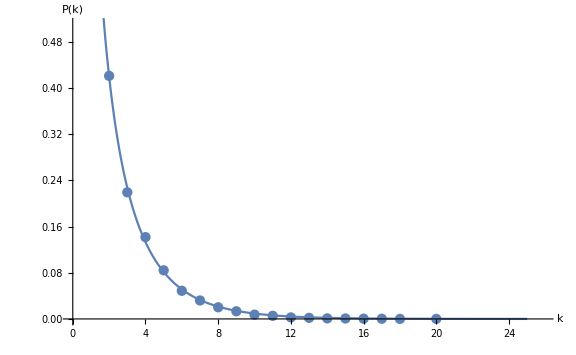

```mathematica
happyOrbitsHVPlot=Show[
ListPlot[happyOrbitsHVDegrees,PlotRange->{{0,25.9},{0,.51}},AxesOrigin->{0,0}],Plot[happyOrbitsHVNlm[x],{x,0,25},PlotRange->Full,AxesOrigin->{0,0}],
AxesLabel-> {Style["k",36, Italic],Style["P(k)", 36,Italic]},LabelStyle->20,ImageSize->Large
]
```

```mathematica
happyOrbitsHVNlm["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
γ | 0.67699 | 0.105101 | {0.452973,0.901008}
c | 1.32232 | 0.0292029 | {1.26008,1.38457}
d | 0.339599 | 0.0323713 | {0.270601,0.408597}

```mathematica
TableForm[
Flatten[{"horizontal visibility",Mean@ VertexDegree[happyOrbitsHVGraph]//N,MeanGraphDistance[happyOrbitsHVGraph]//N,
GlobalClusteringCoefficient[happyOrbitsHVGraph]//N,Mean[happyOrbitsHVNlm["FitResiduals"]^2],ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@happyOrbitsHVNlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}],TableHeadings->{{"algo","⟨k⟩","⟨l_min⟩","C_c","⟨e^2⟩","γ","C","δ"},None},TableDirections->Row]
```

algo | ⟨k⟩ | ⟨l_min⟩ | C_c | ⟨e^2⟩ | γ | C | δ
horizontal visibility | 3.5132 | 15.2123 | 0.271626 | 8.99209×10^-6 | 0.67699 ± 0.224018 | 1.32232 ± 0.0622446 | 0.339599 ± 0.0689978

## Final Results

```mathematica
TableForm[{Flatten[{"natural visibility",Mean@ VertexDegree[happyNVGraph]//N,MeanGraphDistance[happyNVGraph]//N,
GlobalClusteringCoefficient[happyNVGraph]//N,Mean[happyNVNlm["FitResiduals"]^2],ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@happyNVNlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}],
Flatten[{"horizontal visibility",Mean@ VertexDegree[happyHVGraph]//N,MeanGraphDistance[happyHVGraph]//N,
GlobalClusteringCoefficient[happyHVGraph]//N,Mean[happyHVNlm["FitResiduals"]^2],ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@happyHVNlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}],Flatten[{"natural visibility",Mean@ VertexDegree[happyOrbitsNVGraph]//N,MeanGraphDistance[happyOrbitsNVGraph]//N,
GlobalClusteringCoefficient[happyOrbitsNVGraph]//N,Mean[happyOrbitsNVNlm["FitResiduals"]^2],ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@happyOrbitsNVNlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}],Flatten[{"horizontal visibility",Mean@ VertexDegree[happyOrbitsHVGraph]//N,MeanGraphDistance[happyOrbitsHVGraph]//N,
GlobalClusteringCoefficient[happyOrbitsHVGraph]//N,Mean[happyOrbitsHVNlm["FitResiduals"]^2],ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@happyOrbitsHVNlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}]},TableHeadings->{None,{"algo","⟨k⟩","⟨l_min⟩","C_c","⟨e^2⟩","γ","C","δ"}}]
```

algo | ⟨k⟩ | ⟨l_min⟩ | C_c | ⟨e^2⟩ | γ | C | δ
natural visibility | 6.5896 | 6.84412 | 0.354645 | 0.0000115452 | -2.30214 ± 0.219179 | 0.0973184 ± 0.0102194 | 0.675061 ± 0.0512771
horizontal visibility | 3.5132 | 15.2123 | 0.271626 | 8.99209×10^-6 | 0.67699 ± 0.224018 | 1.32232 ± 0.0622446 | 0.339599 ± 0.0689978
natural visibility | 5.3117 | 54.5357 | 0.124025 | 6.82896×10^-6 | -2.12168 ± 0.16285 | 0.193115 ± 0.0114277 | 0.754397 ± 0.0430676
horizontal visibility | 3.5132 | 15.2123 | 0.271626 | 8.99209×10^-6 | 0.67699 ± 0.224018 | 1.32232 ± 0.0622446 | 0.339599 ± 0.0689978